## ML - Jhon Aponte

```mathematica
(*We're gonna understand the problem of surfaces.*)
(*We're gonna cliff the crystal.*)
(*In a crytal, you can have many faces, e.g. (1,1,1)*)
(*For the final, we need to replicate a 2010 Nature paper, about surfaces.*)
(*We're gonna be able to replicate FIG. 31 in the manual.*)
```

```mathematica
(*In the INCAR file, MD -> molecular dynamics.*)
(*We're gonna train a force field for Silicon.*)
```

```mathematica
(*To use ML force fields, first, we need to create the bulk.*)
(*ML force field model -> like a multi dimensional fit.*)
```

```mathematica
(*ml.sh script: POSCAR-222 -> takes previous POSCAR files and makes it 2x2x2.*)
(*Molecular dynamics force fields ensambles -> npt (number of particles, pressure, and temperature cosntant), nvt, at 400 K. *)
```

```mathematica
(*ICONST: if you want to study the thermal expansion of the material (we're not gonna use it here).*)
```

```mathematica
(*INCAR-ml: ISYM = 0 -> to not impose symmetries in the material (always 0 here), IVDW (Van-Der Wall dispersions), POTIM -> time step (here, 2 fs), ! machine learning -> T is training, .*)
```

```mathematica
(*In the folder md, the results-ml.dat file has information about the time it took to run the ml.script.*)
(*In formal work, around 100000 steps are needed.*)
```

```mathematica
(*Important files: ML_ABN (info about the training set), ML_FFN (binary file with the force field we created), ML_LOGFILE (to measure the relative quality of the force field).*)
```

```mathematica
(*When you do ML, you have the training set and the outher set. The Bayesian error is related to the out of the sample error -> prediction of the calculation (relative). The other error is the error of the training set.*)
(*Here, we're training on nergy, forces, and stress (this last one, for seeing the phase transitions).*)
```

```mathematica
wrk="/home/rolando/Downloads/Yachay/8th_Semester/dft/final_exam/scripts_inputs/scripts_inputs/machlearn";
SetDirectory[wrk];
```

```mathematica
paramplot={BaseStyle->{FontFamily->"Helvetica", FontSize->16}, ImageSize->600,Frame->True};
```

### Bayesian Error on the Forces

```mathematica
beef=Import["ml/beef.dat"];
```

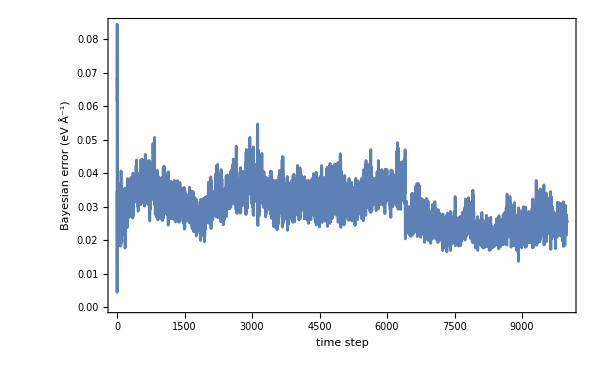

```mathematica
beef//
ListPlot[#,
FrameLabel->{"time step", "Bayesian error (eV Å^-1)"},
Joined->True,
PlotRange->All,
paramplot]&
```

```mathematica
(*This error is from external data (other surfaces data).*)
(*The error is not that big; we should worry when it's around 0.1 or more.*)
(*THis tells us the quality of our prediction.*)
```

```mathematica
err=Import["ml/err.dat"];
```

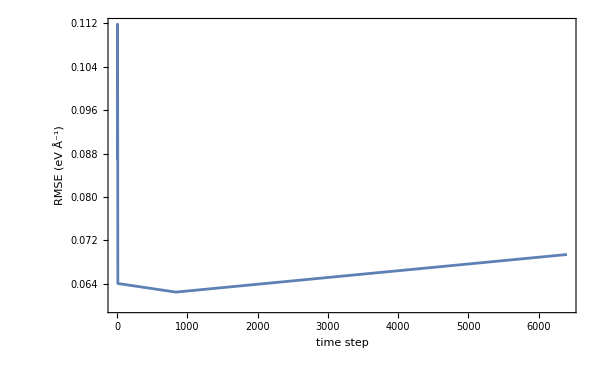

```mathematica
err//
ListPlot[#,
FrameLabel->{"time step", "RMSE (eV Å^-1)"},
Joined->True,
PlotRange->All,
paramplot]&
```

```mathematica
(*This is to see the quality of the inside data.*)
```

### Check the KPOINTS Grid:

```mathematica
sc=Import["POSCAR-222", "Table"];
```

```mathematica
lattsc=sc[[2,1]]×sc[[3;;5]]
```

{{5.05252,0.,0.},{2.52626,4.37561,0.},{2.52626,1.45854,4.12537}}

```mathematica
{a,b,c}=lattsc;
```

```mathematica
Δk=Table[0.15-0.005i,{i,0,15}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/(a.(b×c))//Norm)/#],Round[((a×c)/(a.(b×c))//Norm)/#],Round[((a×b)/(a.(b×c))//Norm)/#]}&,#]&//TableForm
```

0.15 | 2 | 2 | 2
0.145 | 2 | 2 | 2
0.14 | 2 | 2 | 2
0.135 | 2 | 2 | 2
0.13 | 2 | 2 | 2
0.125 | 2 | 2 | 2
0.12 | 2 | 2 | 2
0.115 | 2 | 2 | 2
0.11 | 2 | 2 | 2
0.105 | 2 | 2 | 2
0.1 | 2 | 2 | 2
0.095 | 3 | 3 | 3
0.09 | 3 | 3 | 3
0.085 | 3 | 3 | 3
0.08 | 3 | 3 | 3
0.075 | 3 | 3 | 3

```mathematica
pc=Import["POSCAR-pc", "Table"]
```

{{C},{1.},{2.5145,0.,0.},{1.25725,2.17762,0.},{1.25725,0.725874,2.05308},{2},{Cartesian},{0.,0.,0.},{1.25725,0.725874,0.51327}}

```mathematica
lattsc=pc[[2,1]]pc[[3;;5]]
```

{{2.5145,0.,0.},{1.25725,2.17762,0.},{1.25725,0.725874,2.05308}}

```mathematica
{a,b,c}=lattsc;
```

```mathematica
Δk=Table[0.15-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/(a.(b×c))//Norm)/#],Round[((a×c)/(a.(b×c))//Norm)/#],Round[((a×b)/(a.(b×c))//Norm)/#]}&,#]&//TableForm
```

0.15 | 3 | 3 | 3
0.145 | 3 | 3 | 3
0.14 | 3 | 3 | 3
0.135 | 4 | 4 | 4
0.13 | 4 | 4 | 4
0.125 | 4 | 4 | 4
0.12 | 4 | 4 | 4
0.115 | 4 | 4 | 4
0.11 | 4 | 4 | 4
0.105 | 5 | 5 | 5
0.1 | 5 | 5 | 5

```mathematica
(*Now, we're gonna run the cell-ml.sh and cell-dft.sh scripts.*)
```

### EOS MLFF vs DFT

This is the computed EOS using ML:

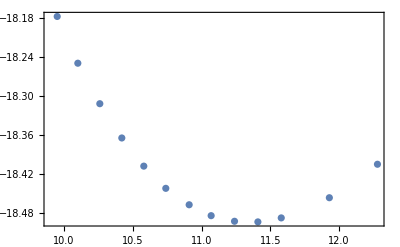

```mathematica
datML=Import["ml/eos-mlPC/cell-ml.dat"];
ListPlot[datML,Frame->True]
```

This is the computed EOS using DFT:

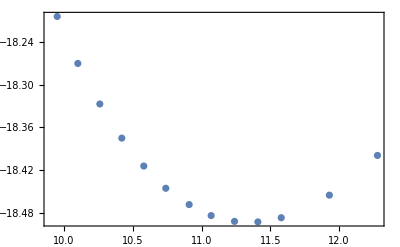

```mathematica
datAB=Import["dft-eosPC/cell-dft.dat"]; (*AB -> ab initio*)
ListPlot[datAB,Frame->True]
```

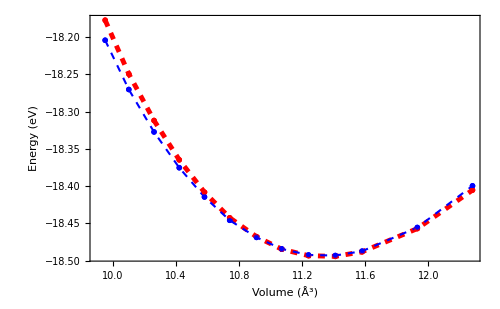

```mathematica
ListLinePlot[{datML,datAB},
Frame->True,
Joined->True,
PlotStyle->{{Red,Thickness[0.007],Dashed},{Blue,Thickness[0.003],Dashed}},
FrameLabel->{"Volume (Å^3)","Energy (eV)"},
PlotLegends->{"MLFF","DFT"},
ImageSize->500,
paramplot,
Mesh->Full,
MeshStyle->PointSize[Small],
PlotMarkers->"OpenMarkers"]
```

```mathematica
(*Both almost match completely, and we used only 10000 training steps.*)
(*The blue plot is the exact one.*)
(*With DFT, it took a couple of minutes, and with ML, it took seconds (without considering the training time).*)
```

```mathematica
(*Now, we're gonna generate our surface.*)
(*POSCAR-bulk (generated in section 4) -> we're gonna transform this file into a .cif file, and then open it in Materials Studio.*)
```

```mathematica
(*Imposing the symmetry means applying the symmetry to the system. For surfaces, we need to work in the unit cell. We start with the primitive cell, but by doing this, we get the unit cell (Important for the exam).*)
```

```mathematica
(*We're just interested in the interaction in the x and y axes, not in the z axis, because in this direction, atoms are isolated. In this direction, we're gonna increase the thickness to see how the energy changes (we need to reach a point in which it doesn't change anymore as a way to see the minimum vacuum we need to build the surface).*)
```

```mathematica
(*The k-points needed to compute this change of energy with the vaccum are already computed in the KPOINTS-ml1x1 file.*)
```

### Check the KPOINTS Grid (slab):

```mathematica
slab=Import["POSCAR-100", "Table"];
```

```mathematica
latt=slab[[2,1]]×slab[[3;;5]]
```

{{2.5263,0.,0.},{0.,2.5263,0.},{0.,0.,13.5727}}

```mathematica
{a,b,c}=latt;
```

```mathematica
Δk=Table[0.15-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/(a.(b×c))//Norm)/#],Round[((a×c)/(a.(b×c))//Norm)/#],Round[((a×b)/(a.(b×c))//Norm)/#]}&,#]&//TableForm
```

0.15 | 3 | 3 | 0
0.145 | 3 | 3 | 1
0.14 | 3 | 3 | 1
0.135 | 3 | 3 | 1
0.13 | 3 | 3 | 1
0.125 | 3 | 3 | 1
0.12 | 3 | 3 | 1
0.115 | 3 | 3 | 1
0.11 | 4 | 4 | 1
0.105 | 4 | 4 | 1
0.1 | 4 | 4 | 1

```mathematica
slab=Import["surf/POSCAR-1x1l5v10", "Table"];
```

```mathematica
latt=slab[[2,1]]×slab[[3;;5]]
```

{{2.5263,0.,0.},{0.,2.5263,0.},{0.,0.,14.5727}}

```mathematica
{a,b,c}=latt;
```

```mathematica
Δk=Table[0.08-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/(a.(b×c))//Norm)/#],Round[((a×c)/(a.(b×c))//Norm)/#],Round[((a×b)/(a.(b×c))//Norm)/#]}&,#]&//TableForm
```

0.08 | 5 | 5 | 1
0.075 | 5 | 5 | 1
0.07 | 6 | 6 | 1
0.065 | 6 | 6 | 1
0.06 | 7 | 7 | 1
0.055 | 7 | 7 | 1
0.05 | 8 | 8 | 1
0.045 | 9 | 9 | 2
0.04 | 10 | 10 | 2
0.035 | 11 | 11 | 2
0.03 | 13 | 13 | 2

```mathematica
(*In the case of ML we need the Δk 0.075, which corresponds to the k-points 3 3 1 (these are in the KPOINTS-ml1x1 file).*)
(*The value of the k-point in z has to always be 1, since we don't want interactions between the slab and the ...*)
```

```mathematica
(*Now, we're gonna run the vacuum.sh script.*)
```

```mathematica
slab=Import["/home/rolando/Downloads/Yachay/8th_Semester/dft/final_exam/scripts_inputs/scripts_inputs/machlearn/surf/POSCAR-2x2c", "Table"];
```

```mathematica
latt=slab[[2,1]]×slab[[3;;5]]
```

{{5.0526,0.,0.},{0.,5.0526,0.},{0.,0.,14.5727}}

```mathematica
{a,b,c}=latt;
```

```mathematica
Δk=Table[0.15-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/(a.(b×c))//Norm)/#],Round[((a×c)/(a.(b×c))//Norm)/#],Round[((a×b)/(a.(b×c))//Norm)/#]}&,#]&//TableForm
```

0.15 | 1 | 1 | 0
0.145 | 1 | 1 | 0
0.14 | 1 | 1 | 0
0.135 | 1 | 1 | 1
0.13 | 2 | 2 | 1
0.125 | 2 | 2 | 1
0.12 | 2 | 2 | 1
0.115 | 2 | 2 | 1
0.11 | 2 | 2 | 1
0.105 | 2 | 2 | 1
0.1 | 2 | 2 | 1

```mathematica
slab=Import["/home/rolando/Downloads/Yachay/8th_Semester/dft/final_exam/scripts_inputs/scripts_inputs/machlearn/mls/CONTCAR", "Table"];
```

```mathematica
latt=slab[[2,1]]×slab[[3;;5]]
```

{{5.0526,0.,0.},{0.,5.0526,0.},{0.,0.,14.5727}}

```mathematica
{a,b,c}=latt;
```

```mathematica
Δk=Table[0.15-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/(a.(b×c))//Norm)/#],Round[((a×c)/(a.(b×c))//Norm)/#],Round[((a×b)/(a.(b×c))//Norm)/#]}&,#]&//TableForm
```

0.15 | 1 | 1 | 0
0.145 | 1 | 1 | 0
0.14 | 1 | 1 | 0
0.135 | 1 | 1 | 1
0.13 | 2 | 2 | 1
0.125 | 2 | 2 | 1
0.12 | 2 | 2 | 1
0.115 | 2 | 2 | 1
0.11 | 2 | 2 | 1
0.105 | 2 | 2 | 1
0.1 | 2 | 2 | 1

```mathematica
(*In the case of ML we need the Δk 0.075, which corresponds to the k-points 3 3 1 (these are in the KPOINTS-ml1x1 file).*)
(*The value of the k-point in z has to always be 1, since we don't want interactions between the slab and the ...*)
```

```mathematica
slab=Import["/home/rolando/Downloads/Yachay/8th_Semester/dft/final_exam/scripts_inputs/scripts_inputs/machlearn/sa/CONTCAR-2x2l5v10.rxo", "Table"];
```

```mathematica
latt=slab[[2,1]]×slab[[3;;5]]
```

{{5.0526,0.,0.},{0.,5.0526,0.},{0.,0.,14.5727}}

```mathematica
{a,b,c}=latt;
```

```mathematica
Δk=Table[0.08-0.005i,{i,0,10}];
```

```mathematica
Δk//Map[{#,Round[((b×c)/(a.(b×c))//Norm)/#],Round[((a×c)/(a.(b×c))//Norm)/#],Round[((a×b)/(a.(b×c))//Norm)/#]}&,#]&//TableForm
```

0.08 | 2 | 2 | 1
0.075 | 3 | 3 | 1
0.07 | 3 | 3 | 1
0.065 | 3 | 3 | 1
0.06 | 3 | 3 | 1
0.055 | 4 | 4 | 1
0.05 | 4 | 4 | 1
0.045 | 4 | 4 | 2
0.04 | 5 | 5 | 2
0.035 | 6 | 6 | 2
0.03 | 7 | 7 | 2

### The Change of Energy per Atom vs Vacuum Size

```mathematica
vac=Import["surf/vacuum.dat"]//Map[#/{1,5}&,#]& (*The system has 5 atoms.*)
```

{{5.,-9.02255},{6.,-9.02557},{7.,-9.02415},{8.,-9.02408},{9.,-9.02408},{10.,-9.02408},{11.,-9.02408},{12.,-9.02408},{13.,-9.02408},{14.,-9.02408},{15.,-9.02408}}

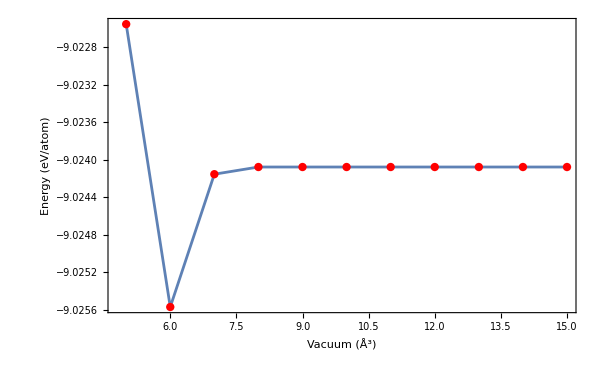

```mathematica
ListPlot[vac,
Frame->True,
FrameLabel->{"Vacuum (Å^3)","Energy (eV/atom)"},
Axes->False,
paramplot,
PlotRange->All,
Joined->True,
Epilog->{Red,AbsolutePointSize[6],Point[vac]}
]
```

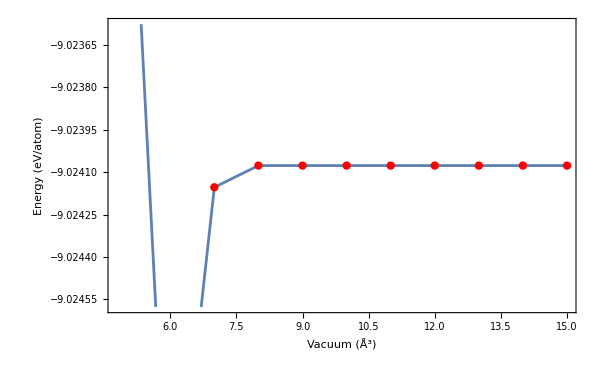

```mathematica
vac//ListPlot[#,
Frame->True,
FrameLabel->{"Vacuum (Å^3)","Energy (eV/atom)"},
Axes->False,
paramplot,
Joined->True,
Epilog->{Red,AbsolutePointSize[6],Point[#]},
PlotRange->{#[[-1,2]]-0.5*10^-3,#[[-1,2]]+0.5*10^-3}
]&
```

```mathematica
(*We get convergency from around 8 Å^3, so we need to use a vacuum of at least 8 Å^3. But since we're gonna compute the STM images, we're gonna use 11 Å^3.*)
```

```mathematica
(*Now, we're gonna passivate the surface*)
```

### Surface Energies

```mathematica
surfen=Import["surf/surfaces.dat"][[All,{1,2}]];
```

```mathematica
surfen//TableForm
```

2x2l5v10 | -195.412

```mathematica
A2x2=7.73420^2;
e[Si]=-5.4240;
e[H]=-3.3795;
area={A2X2};
(*The values of the energies (e) are in the manual.*)
(*The value of the area is in the CONTCAR-2x2l5v10.rx file*)
```

```mathematica
nsi=20;
nh=8;
```

```mathematica
1/(2 A2x2) (Eslab-nsi e[Si]-nh e[H])/.Eslab->surfen[[1,2]]
```

0.0541296

```mathematica
(*This is the energy of our system, in eV/Å^2*)
```

### DOS of Si (100) Surface

```mathematica
input=Import["surf/DOSCAR-2x2l5v10.st", "Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
ef=input[[6,4]]
```

0.69671

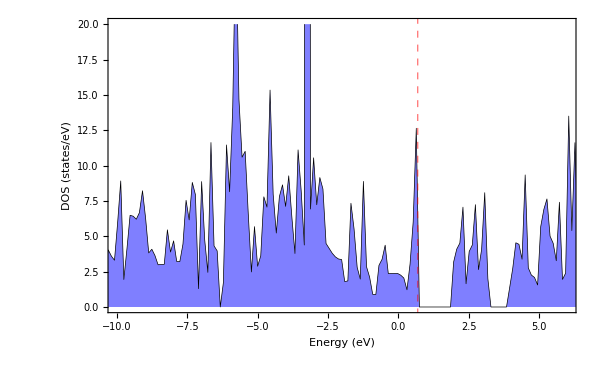

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
GridLines->{{ef},None},
GridLinesStyle->Directive[Red, Dashed],
paramplot,
PlotRange->{{-10,6},{0,20}},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black}
]
```

```mathematica
(*This is the density of states of the surface, and we can see a band gap (remember that the bulk system also had a band gap).*)
```

### Generation of STM Images for Si(100)-2×2

```mathematica
in=Import["surf/PARCHG-2x2l5v10_2.5.vasp", "Table"];
```

```mathematica
numat=Plus@@in[[7]]
```

28

```mathematica
thelattice=in[[3;;5]]
```

{{5.0526,0.,0.},{0.,5.0526,0.},{0.,0.,14.5727}}

```mathematica
in[[7+numat+3]]
```

{72,72,216}

```mathematica
stm=(in[[7+numat+4;;-1]]//Flatten);
```

```mathematica
stm//Dimensions
```

{1119744}

```mathematica
stm[[1]]
```

2.0531

```mathematica
stm[[-1]]
```

2.447

```mathematica
divX=in[[7+numat+3,1]]
```

72

```mathematica
divY=in[[7+numat+3,2]]
```

72

```mathematica
zrange=in[[5,{2,3}]]
```

{0.,14.5727}

```mathematica
transformDATA=
(
#
//Partition[#,divX]&
//Partition[#,divY]&
//Map[Append[#,First[#]]&,#,{2}]&
//Map[Append[#,First[#]]&,#]&
//Transpose[#,{3,2,1}]&
)&;
```

```mathematica
stm1=stm//transformDATA;
```

```mathematica
stm1[[1,1]][[1]]
```

2.0531

```mathematica
stm1//Dimensions
```

{73,73,216}

#### Here the interpolation for stm1

```mathematica
theInterpolation=ListInterpolation[#,{{0,in[[3,1]]},{0,in[[4,2]]},{0,in[[5,3]]}},PeriodicInterpolation->{True,True,False}]&;
```

```mathematica
stminterpolation=stm1//theInterpolation;
```

```mathematica
stminterpolation[0,0,3]
```

1.07518

```mathematica
nx=2;
ny=2;
```

```mathematica
nx=2;
ny=2;
ContourPlot3D[stminterpolation[x,y,z]==0.05,
{x,0,nx thelattice[[1,1]]},
{y,0,ny thelattice[[2,2]]},
{z,5,8.5},
ColorFunction->Function[{x,y,z,f}, ColorData["SunsetColors"][z]],
PlotPoints->30,
MaxRecursion->0,
BoxRatios->{1,(ny thelattice[[2,2]])/(nx thelattice[[1,1]]),(8.5-5)/(nx thelattice[[1,1]])},
AxesLabel->{"x(Å)","y(Å)",None},
ViewPoint->{0,0,∞},
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
ContourStyle->Directive[Opacity[1.]],
Lighting->AmbientLight[GrayLevel[1.]],
Mesh->None]
```

-Graphics3D-

```mathematica
in=Import["surf/PARCHG-2x2l5v10-2.vasp", "Table"];
```

```mathematica
numat=Plus@@in[[7]]
```

28

```mathematica
thelattice=in[[3;;5]]
```

{{5.0526,0.,0.},{0.,5.0526,0.},{0.,0.,14.5727}}

```mathematica
in[[7+numat+3]]
```

{72,72,216}

```mathematica
stm=(in[[7+numat+4;;-1]]//Flatten);
```

```mathematica
stm//Dimensions
```

{1119744}

```mathematica
stm[[1]]
```

0.60299

```mathematica
stm[[-1]]
```

0.58611

```mathematica
divX=in[[7+numat+3,1]]
```

72

```mathematica
divY=in[[7+numat+3,2]]
```

72

```mathematica
zrange=in[[5,{2,3}]]
```

{0.,14.5727}

```mathematica
transformDATA=
(
#
//Partition[#,divX]&
//Partition[#,divY]&
//Map[Append[#,First[#]]&,#,{2}]&
//Map[Append[#,First[#]]&,#]&
//Transpose[#,{3,2,1}]&
)&;
```

```mathematica
stm1=stm//transformDATA;
```

```mathematica
stm1[[1,1]][[1]]
```

0.60299

```mathematica
stm1//Dimensions
```

{73,73,216}

#### Here the interpolation for stm1

```mathematica
theInterpolation=ListInterpolation[#,{{0,in[[3,1]]},{0,in[[4,2]]},{0,in[[5,3]]}},PeriodicInterpolation->{True,True,False}]&;
```

```mathematica
stminterpolation=stm1//theInterpolation;
```

```mathematica
stminterpolation[0,0,3]
```

25.0803

```mathematica
nx=2;
ny=2;
ContourPlot3D[stminterpolation[x,y,z]==0.05,
{x,0,nx thelattice[[1,1]]},
{y,0,ny thelattice[[2,2]]},
{z,5,8.5},
ColorFunction->Function[{x,y,z,f}, ColorData["SunsetColors"][z]],
PlotPoints->30,
MaxRecursion->0,
BoxRatios->{1,(ny thelattice[[2,2]])/(nx thelattice[[1,1]]),(8.5-5)/(nx thelattice[[1,1]])},
AxesLabel->{"x(Å)","y(Å)",None},
ViewPoint->{0,0,∞},
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
ContourStyle->Directive[Opacity[1.]],
Lighting->AmbientLight[GrayLevel[1.]],
Mesh->None]
```

-Graphics3D-